Set directory

```mathematica
NotebookDirectory[]
SetDirectory[" "]
```

RWA without A^2

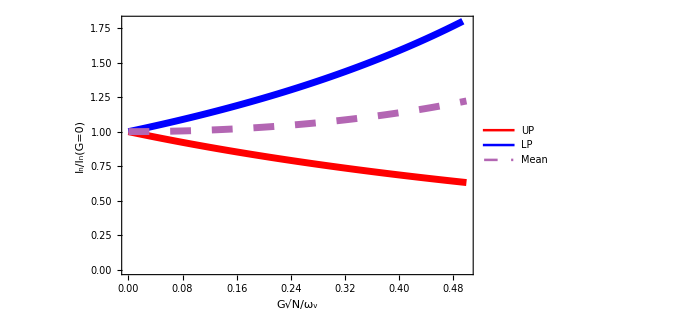

```mathematica
Ω=100.; (* vibr energy in meV *)
NN=1000000.; (*total number of molecules *)
wc=100.; (* cavity photon energy in meV *)
S=0.3; (*electronic transition - vibration coupling*)
Δ = 100.; (*electronic transition - laser frequency detuning*)

Pr1 = {};
Pr2 = {};

Do[
 
w = wc{1 + coupl, 1 - coupl, 1};
au[j_]:= wc^2(Exp[-z w[[j]]] - 1)/w[[j]]^2{1,1,2(NN-1)};
Prob[i_]:= (S NN)/2*(wc/w[[i]])^2 Abs[NIntegrate[Exp[-z Δ](Exp[-z w[[i]]]-1)Exp[-S/(2NN)Sum[au[j][[j]],{j,1,3}]],{z,0,Infinity}]]^2;
AppendTo[Pr1,{coupl,Prob[1]}];
AppendTo[Pr2,{coupl,Prob[2]}];,
{coupl,0.0001,0.5001,0.01}];

Pr1[[All,2]]=Pr1[[All,2]]/Pr1[[1,2]];(*normalization by the probability without light-matter coupling*)
Pr2[[All,2]]=Pr2[[All,2]]/Pr2[[1,2]];
Tot = (Pr1 + Pr2)/2;
Probmain = {Pr1,Pr2,Tot};
ListLinePlot[Probmain,PlotLegends->Placed[{"UP","LP","Mean"},{0.15,0.8}], AxesStyle->Directive[Black],PlotStyle->{Directive[Red,Thickness[0.01]],Directive[Blue,Thickness[0.01]],Directive[Lighter[Purple,0.4],Thickness[0.01],Dashing[0.03]]},Frame->True,FrameTicks->{{All,Automatic},{All,Automatic}},FrameTicksStyle->Directive[Black,17],AspectRatio->0.65,FrameLabel->{Style["G√N/ω_v",FontTracking->"Narrow",FontFamily->"Times",FontSlant->Plain],Style["P_n/P_n(G=0)",FontTracking->"Narrow",FontFamily->"Times",FontSlant->Plain]},LabelStyle->{Black,20,FontFamily->"Times"},DataRange->{0,0.5},ImageSize->500,PlotRangePadding->0,PlotRange->{0,1.8}]


Export["pr_RWA.txt",Probmain];
```

RWA, vibron - photon detuning (for two values of Rabi splitting)

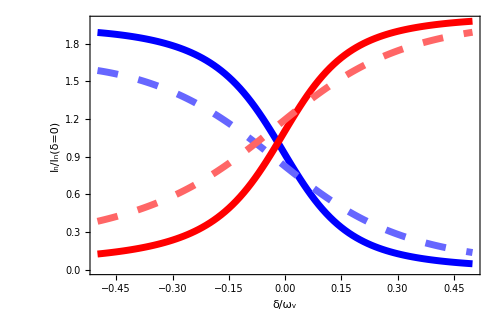

```mathematica
Ω=100.; (* vibr energy in meV *)
NN=1000000.; (*total number of molecules *)
S=0.3; (*electron transition - vibration coupling*)
Δ = 100.;(*electronic transition - laser frequency detuning*)
Pr1 = {};
Pr2 = {};
Pr3 = {};
Pr4 = {};
(* coupl = G√N/Subscript[ω, v] *)
coupl = 10^(-6);
delt = 0;
w = Ω{1 + delt/(2 Ω) + Sqrt[delt^2/(4 Ω^2)+ coupl^2], 1 + delt/(2 Ω) - Sqrt[delt^2/(4 Ω^2)+ coupl^2], 1};
U = coupl{1/Sqrt[((w[[1]] - Ω)/Ω)^2 + coupl^2],1/Sqrt[((w[[2]] - Ω)/Ω)^2 + coupl^2]};
bet = Sqrt[S]Ω{U[[1]]/w[[1]],U[[2]]/w[[2]]};
au[j_]:= (Exp[-z w[[j]]] - 1){bet[[1]]^2,bet[[2]]^2,S/NN(NN-1)};
Prob[i_]:= NN Abs[bet[[i]]NIntegrate[Exp[-z Δ](Exp[-z w[[i]]]-1)Exp[Sum[au[j][[j]],{j,1,3}]],{z,0,Infinity}]]^2;
norm = Prob[1];


Do[Do[
delt = deltt*Ω;
w = Ω{1 + delt/(2 Ω) + Sqrt[delt^2/(4 Ω^2)+ coupl^2], 1 + delt/(2 Ω) - Sqrt[delt^2/(4 Ω^2)+ coupl^2], 1};

U = coupl{1/Sqrt[((w[[1]] - Ω)/Ω)^2 + coupl^2],1/Sqrt[((w[[2]] - Ω)/Ω)^2 + coupl^2]};
bet = Sqrt[S]Ω{U[[1]]/w[[1]],U[[2]]/w[[2]]};



au[j_]:= (Exp[-z w[[j]]] - 1){bet[[1]]^2,bet[[2]]^2,S/NN(NN-1)};

Prob[i_]:= NN Abs[bet[[i]]NIntegrate[Exp[-z Δ](Exp[-z w[[i]]]-1)Exp[Sum[au[j][[j]],{j,1,3}]],{z,0,Infinity}]]^2;
If[coupl==0.1,
AppendTo[Pr1,{deltt,Prob[1]/norm}];
AppendTo[Pr2,{deltt,Prob[2]/norm}];,
AppendTo[Pr3,{deltt,Prob[1]/norm}];
AppendTo[Pr4,{deltt,Prob[2]/norm}]],
{deltt,-0.5,0.5,0.01}];,{coupl,0.1,0.2,0.1}]


Detuning = {Pr1,Pr2,Pr3,Pr4};

ListLinePlot[Detuning,AxesStyle->Directive[Black],PlotStyle->{Directive[Blue,Thickness[0.01]],Directive[Red,Thickness[0.01]],Directive[Lighter[Blue,0.4],Thickness[0.01],Dashing[0.03]],Directive[Lighter[Red,0.4],Thickness[0.01],Dashing[0.03]]},Frame->True,FrameTicks->{{All,Automatic},{All,Automatic}},FrameTicksStyle->Directive[Black,17],AspectRatio->0.65,FrameLabel->{Style["δ/ω_v",FontSlant->Plain,FontTracking->"Narrow"],Style["P_n/P_n(G=0;δ=0)",FontSlant->Plain]},LabelStyle->{Black,20,FontFamily->"Times",FontSlant->Plain},ImageSize->500,PlotRangePadding->0]

Export["scat1_detuning_rabi.txt",Detuning];
```

non RWA with A^2 SCATTERING PROBABILITIES; δω_v= 0

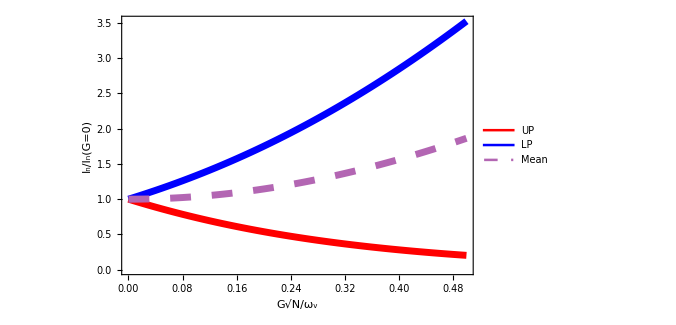

```mathematica
Ω=100.; (* vibr energy in meV *)
NN=1000000.; (*total number of molecules *)
wc=100.; (* cavity photon energy in meV *)
S=0.3; (*electron transition - vibration coupling*)
Δ = 100.;(*electronic transition - laser frequency detuning*)

Pr1 = {};
Pr2 = {};

h={0, Ω Sqrt[2 Ω S],0};
fhelp[x_]:= 1/x^2/;x!=0 ;
fhelp[0]= 0;


Do[
G=(coupl*Ω)/Sqrt[NN]; (* light-vib coupling *)    
ξ=2G Sqrt[wc Ω ];
V=({{wc^2+ 4 G^2 NN, ξ, ξ*Sqrt[NN-1]}, {ξ, Ω^2, 0}, {ξ*Sqrt[NN-1], 0, Ω^2}});
U=Chop[ConjugateTranspose[Normalize/@Eigenvectors[V]]];
omega = Sqrt[Chop[ConjugateTranspose[U].V.U]];
ω=Diagonal@omega;
l = Map[fhelp,omega,{2}].Transpose[U].h;
Prob[i_]:=NN( Sqrt[ω[[i]]]/Sqrt[2] l[[i]]NIntegrate[Exp[-s Δ](Exp[- s ω[[i]]] - 1)Exp[-1/2 Sum[l[[j]]^2ω[[j]](1 - Exp[-s ω[[j]]]),{j,1,3}]],{s,0,Infinity}])^2;
AppendTo[Pr1,{coupl,Prob[1]}];
AppendTo[Pr2,{coupl,Prob[3]}];,
{coupl,0.0001,0.5001,0.01}];

Pr1[[All,2]]=Pr1[[All,2]]/Pr1[[1,2]]; (*normalization by the probability without light-matter coupling*)
Pr2[[All,2]]=Pr2[[All,2]]/Pr2[[1,2]];

Tot = (Pr1 + Pr2)/2;
Alldat = {Pr1,Pr2,Tot};
ListLinePlot[Alldat,PlotLegends->Placed[{"UP","LP","Mean"},{0.15,0.8}], AxesStyle->Directive[Black],PlotStyle->{Directive[Red,Thickness[0.01]],Directive[Blue,Thickness[0.01]],Directive[Lighter[Purple,0.4],Thickness[0.01],Dashing[0.03]]},Frame->True,FrameTicks->{{All,Automatic},{All,Automatic}},FrameTicksStyle->Directive[Black,17],AspectRatio->0.65,FrameLabel->{Style["G√N/ω_v",FontSlant->Plain,FontTracking->"Narrow"],Style["I_n/I_n(G=0)",FontSlant->Plain]},LabelStyle->{Black,20,FontFamily->"Times",FontSlant->Plain},DataRange->{0,0.5},ImageSize->500,PlotRangePadding->0]
Export["scatt_non_RWA_withAsquared.txt",Alldat];
```

non RWA with A^2 SCATTERING PROBABILITIES; δω_v≠ 0

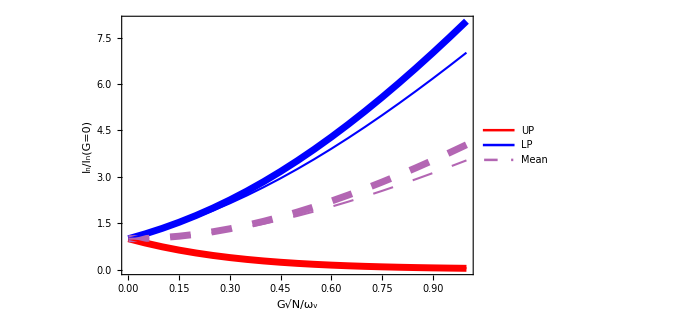

```mathematica
Pr1 = {};
Pr2 = {};
Ω=100.; (* vibr energy in meV *)
NN=1000000.; (*total number of molecules *)
wc=100.; (* cavity photon energy in meV *)
S=0.3; (*electron transition - vibration coupling*)
Δ = 100.;(*normalization by the probability without light-matter coupling*)
fhelp[x_]:= 1/x^2/;x!=0 ; (* auxiliary function *)
fhelp[0]= 0;
hup={0, Ω Sqrt[2 Ω S],0};

Do[Do[
δ = 0.25Ω(2 dev/Ω + (dev/Ω)^2);

G=(coupl*Ω)/Sqrt[NN]; (* light-vib coupling *)    

ξ=2G Sqrt[wc Ω ];

Vdown=({{wc^2 + 4G^2 NN, ξ, ξ*Sqrt[NN-1]}, {ξ, Ω^2, 0}, {ξ*Sqrt[NN-1], 0, Ω^2}});
Vup=Vdown + ({{0, 0, 0}, {0, 4Ω  δ, 0}, {0, 0, 0}});
Uup=Chop[ConjugateTranspose[Normalize/@Eigenvectors[Vup]]]; (* up unitary dioganalization matrix *)
Udown=Chop[ConjugateTranspose[Normalize/@Eigenvectors[Vdown]]]; (* down unitary dioganalization matrix *)
Ωup = Sqrt[Chop[ConjugateTranspose[Uup].Vup.Uup]]; (* up dioganalized matrix *)
Ωdown = Sqrt[Chop[ConjugateTranspose[Udown].Vdown.Udown]]; (* down dioganalized matrix *)
ωdown=Diagonal@Ωdown;
ωup=Diagonal@Ωup;



R = Transpose[Uup].Udown.Ωdown.Transpose[Udown].Uup;
l = Map[fhelp,Ωup,{2}].Transpose[Uup].hup;
P = Chop@DiagonalMatrix[{ωup[[1]]/Tanh[s ωup[[1]]],ωup[[2]]/Tanh[s ωup[[2]]],ωup[[3]]/Tanh[s ωup[[3]]]}];
Q = Chop@DiagonalMatrix[{ωup[[1]]/Sinh[s ωup[[1]]],ωup[[2]]/Sinh[s ωup[[2]]],ωup[[3]]/Sinh[s ωup[[3]]]}];


A = Chop@ArrayFlatten@{{ P + R,-Q},{-Q, P + R}};
q = Chop@Flatten@{l.R,l.R};

 c = l.R.l;

aux = Transpose[Udown].Uup;
ll = Flatten@{l,l};
vec = Inverse[A].q - ll;
vec1 = vec[[1;;3]];
aux1 = Transpose[Udown].Uup.vec1;
Prob[i_]:=NN Re[8 Sqrt[2 ωdown[[i]]] Exp[-c]NIntegrate[Exp[-s Δ]Product[Sqrt[(ωdown[[j]]ωup[[j]])/(1 - Exp[-2 s ωup[[j]]])],{j,1,3}]*Exp[1/2 q.Inverse[A].q]/Sqrt[Det[A]] aux1[[i]],{s,0,Infinity},Method->"LocalAdaptive"]]^2;
AppendTo[Pr1,{coupl,Prob[1]}];
AppendTo[Pr2,{coupl,Prob[3]}];,
{coupl,0.001,1.001,0.05}],{dev,-50,0,50}]

Pr11=Pr1[[;;21,2]]/Pr1[[1,2]];(*normalization by the probability without light-matter coupling*)
Pr21=Pr2[[;;21,2]]/Pr2[[1,2]];
Totpr1 = (Pr11+Pr21)/2;


Pr12=Pr1[[22;;,2]]/Pr1[[22,2]];
Pr22=Pr2[[22;;,2]]/Pr2[[22,2]];
Totpr2 = (Pr12+Pr22)/2;

Alldat1 = {Pr12,Pr22,Totpr2,Pr11,Pr21,Totpr1};
ListLinePlot[{Pr12,Pr22,Totpr2,Pr11,Pr21,Totpr1},PlotLegends->Placed[{"UP","LP","Mean"},{0.15,0.8}], AxesStyle->Directive[Black],PlotStyle->{
Directive[Red,Thickness[0.01]],Directive[Blue,Thickness[0.01]],Directive[Lighter[Purple,0.4],Thickness[0.01],Dashing[0.03]],
Directive[Red,Thickness[0.003]],Directive[Blue,Thickness[0.003]],Directive[Lighter[Purple,0.4],Thickness[0.003],Dashing[0.03]]},
Frame->True,FrameTicks->{{All,Automatic},{All,Automatic}},FrameTicksStyle->Directive[Black,17],AspectRatio->0.65,FrameLabel->{Style["G√N/ω_v",FontTracking->"Narrow"],Style["P_n/P_n(G=0)"]},LabelStyle->{Black,20,FontFamily->"Times"},DataRange->{0,1},ImageSize->500,PlotRangePadding->0]
05
Export["scatt_non_RWA_withAsquared_nonzero_detun.txt",Alldat1];
```